# Extremal Radial

Numerically computes the extremal radial solutions using the SN trans

## Config and imports

```mathematica
PREC=16; (* working precision *)
```

```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

## Radial Eq

```mathematica
Δ=r^2-2M*r+a^2;
kext=ω-m/(2M);
eqR=Δ^-s*D[Δ^(s+1)*D[R[r],r],r]+((K^2-2*I*s*(r-M)*K)/Δ+4*I*s*ω*r-λ)*R[r]/.K->(r^2+a^2)*ω-a*m;
eqR/.a->M/.R->Function[r,(-1)^s*(r-M)^(-2s-2I*ω*M)*Exp[(2I*kext*M^2)/(r-M)]*yin[r]]/.yin->Function[r,yin[r/M-1]]/.r->M(1+R)//Simplify;
eqyin=Collect[R^2*%/Coefficient[%,yin''[R]],{yin[R],yin'[R],yin''[R]}];
eqR/.a->M/.R->Function[r,(r-M)^(2I*ω*M)*Exp[-(2I*kext*M^2)/(r-M)]*yout[r]]/.yout->Function[r,yout[r/M-1]]/.r->M(1+R)//Simplify;
ℒ[y]==(eqyout=Collect[R^2*%/Coefficient[%,yout''[R]],{yout[R],yout'[R],yout''[R]}])
```

ℒ[y]==(-λ+M ω (2 ⅈ-2 m+2 ⅈ (2+R) s+4 M ω+4 M R ω+M R^2 ω)) yout[R]+2 (-ⅈ m+2 ⅈ M ω+R (1+s+2 ⅈ M ω)) yout'[R]+R^2 yout''[R]

#### Sep const/eigenvalue: λ=E-2amω+(aω)^(2-)-s(s+1)

```mathematica
λT[s_,l_?IntegerQ,m_?IntegerQ,ω_?NumericQ,a_]=If[a==0,N[l(l+1)-s(s+1),prec],SpinWeightedSpheroidalEigenvalue[s,l,m,N[a ω,16]] -2 m a ω +a^2 ω^2-s(s+1)](*][[1]]]*);
```

## Radial Solutions

## Solvers

```mathematica
RouterBoundary=200;
```

```mathematica
(* generate the asymptotic solutions *)
Clear[yinAsym,youtAsym,yinSolver,youtSolver,yinSolverInterp,youtSolverInterp]

yinAsym=AsymptoticDSolveValue[{eqyin==0,yin[0]==1},yin[R],{R,0,5}];
youtAsym=AsymptoticDSolveValue[{eqyout==0,yout[0]==1},yout[R],{R,0,5}];

yinSolver[sval_,lval_,mval_,ωhatval_,λval_,ϵ_]:=Block[{M=1},
With[{yinval=yinAsym/.R->ϵ,yinp=D[yinAsym,R]/.R->ϵ},
First@NDSolve[{eqyin==0,yin'[ϵ]==yinp,yin[ϵ]==yinval}/.{s->sval,l->lval,m->mval,ω->(ωhatval+mval)/(2M),λ->λval},yin,{R,ϵ,RouterBoundary}]]]
youtSolver[sval_,lval_,mval_,ωhatval_,λval_,ϵ_]:=Block[{M=1},
With[{youtval=youtAsym/.R->ϵ,youtp=D[youtAsym,R]/.R->ϵ},
First@NDSolve[{eqyout==0,yout'[ϵ]==youtp,yout[ϵ]==youtval}/.{s->sval,l->lval,m->mval,ω->(ωhatval+mval)/(2M),λ->λval},yout,{R,ϵ,RouterBoundary}]]]

yinSolverInterp[sval_,lval_,mval_,ωhatval_,λval_,ϵ_]:=Block[{M=1},With[{yinval=yinAsym/. R->ϵ,yinp=D[yinAsym,R]/. R->ϵ},NDSolveValue[{eqyin==0,y'[ϵ]==yinp,y[ϵ]==yinval}/. {s->sval,l->lval,m->mval,ω->(ωhatval+mval)/(2 M),λ->λval},y,{R,ϵ,100}]]]

youtSolverInterp[sval_,lval_,mval_,ωhatval_,λval_,ϵ_]:=Block[{M=1},With[{youtval=youtAsym/. R->ϵ,youtp=D[youtAsym,R]/. R->ϵ},NDSolveValue[{eqyout==0,y'[ϵ]==youtp,y[ϵ]==youtval}/. {s->sval,l->lval,m->mval,ω->(ωhatval+mval)/(2 M),λ->λval},y,{R,ϵ,100}]]]
```

### Tests

```mathematica
Clear[ωhat,ωhatval,ω,yin,yout,genySols]
```

```mathematica
M=1;
stest=2;
ltest=3;
mtest=1;
(*ωtest=1/(10*M);*)

Clear[genSols,genySols]
genySols[s_,l_,m_,ω_]:=Module[{ωhat,λ,yinsol,youtsol,ϵ,r,kLoc,yin,yout},
ωhat=2M ω-m;
kLoc=ω-m/(2M);
λ=λT[s,l,m,ω,M]//N;
ϵ=10^-8;
yinsol=yinSolver[s,l,m,ωhat,λ,ϵ];
youtsol=youtSolver[s,l,m,ωhat,λ,ϵ];
<|"s"->s,"l"->l,"m"->m,"ω"->ω,"y"->yinsol,"yp"->youtsol|>
]

genRSols[s_,l_,m_,ω_]:=Module[{ωhat,λ,yinsol,youtsol,ϵ,r,kLoc,Rinsol,Routsol},ωhat=2 M ω-m;
kLoc=ω-m/(2 M);
λ=λT[s,l,m,ω,M]//N;
ϵ=10^-8;
yinsol=yinSolver[s,l,m,ωhat,λ,ϵ];
youtsol=youtSolver[s,l,m,ωhat,λ,ϵ];
Rinsol=((-1)^s*(r-M)^(-2 s-2 I*ω*M)*Exp[(2 I*kLoc*M^2)/(r-M)]/. r->M*(1+R))*yin[R]/. yinsol;
Routsol=((r-M)^(2 I*ω*M)*Exp[-(2 I*kLoc*M^2/(r-M))]/. r->M*(1+R))*yout[R]/. youtsol;
<|"s"->s,"l"->l,"m"->m,"ω"->ω,"Rin"->Rinsol,"Rout"->Routsol|>]


sol=genRSols[2,3,1,201/400];
```

```mathematica
sol["Rin"]
```

ⅇ^(ⅈ/200/R) R^(-4-(201 ⅈ)/200) InterpolatingFunction[…][R]

```mathematica
ϵtiny=10^-5
```

1/100000

```mathematica
rinExpr=sol["Rin"];
routExpr=sol["Rout"];
```

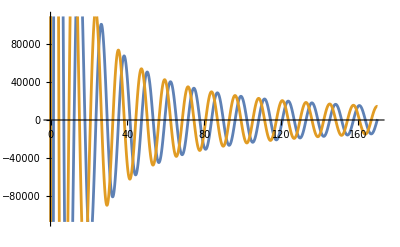

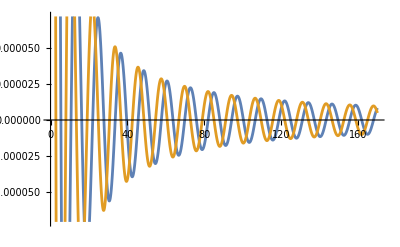

```mathematica
Plot[Evaluate[{Re[rinExpr],Im[rinExpr]}],{R,ϵtiny,170}]
Plot[Evaluate[{Re[routExpr],Im[routExpr]}],{R,ϵtiny,170}]
```

## Greybody Factors

```mathematica
ClearAll[rPlus,OmegaH,kH,epsH,CStarSq,dSN,alphaGW,GBfromAinSN];
```

### spin=-2 conversion from amplitude to GB factor

```mathematica
(* |C_{lmω}|^2,i.e.the squared Starobinsky-Churilov constant 
*)CStarSq[λ_,ω_,m_,a_,M_]:=((λ+2)^2+4 a ω m-4 a^2 ω^2)*(λ^2+36 a ω m-36 a^2 ω^2)+48 a ω (2 λ+3) (2 a ω-m)+144 ω^2 (M^2-a^2);

(*horizon-flux prefactor α_{lmω}*)
alphaGW[λ_,ω_,m_,a_,M_]:=Module[{rp=rPlus[a,M],k=kH[ω,m,a,M],eps=epsH[a,M]},256 (2 M rp)^5 k (k^2+4 eps^2) (k^2+16 eps^2) ω^3/CStarSq[λ,ω,m,a,M]];

(*Greybody factor from the fitted SN incoming amplitude at infinity.Assumes the SN solution is normalized as X~exp[-I k r*] at the horizon,i.e.AtransSN=1.*)

GBfromAmplitudeSN[AinSN_,λ_,ω_,m_,a_,M_]:=Module[{rp,kH,OmH, epsH,C2,dSN,αGW,conversion},
rp=M+Sqrt[M^2-a^2];
OmH:=a/(2 M rp);
kH-m OmH;
epsH=Sqrt[M^2-a^2]/(4 M rp);
C2=CStarSq[λ,ω,m,a,M];
(*d_{lmω}=Γ_{H,-}^{-1}*)
dSN=8 Sqrt[2 M rp] (rp-M-2 I k M rp) (rp-M-I k M rp);
αGW=alphaGW[λ,ω,m,a,M];
conversion=αGW*Abs[4 ω^2/(dSN AinSN)]^2;
conversion
]

(*Extremal Kerr helper:just set a=M*)
GBfromAinSNExtremal[AinSN_,λ_,ω_,m_,M_]:=GBfromAmplitudeSN[AinSN,λ,ω,m,M,M];
```

## Sasaki Nakamura for spin-2

```mathematica
(* Sasaki Nak transformation see https://emis.dsd.sztaki.hu/journals/LRG/Articles/lrr-2003-6/download/lrr-2003-6BW.pdf*)
```

```mathematica
ClearAll[DeltaEx,KEx,etaSNEx,betaSNEx,alphaSNEx,FsnEx,GsnEx,VTEx,U1snEx,UsnEx,VeffREx,xOfREx,rGuessEx,rOfXEx,VeffXEx,lamSNEx];
(*If  angular routine returns the spheroidal eigenvalue E_{lm},this is Hughes' lambda for s=-2. Adjust depending on conventions *)

lamSNEx[l_,m_,om_,M_]:=SpinWeightedSpheroidalEigenvalue[-2,l,m,M om]-2 M m om+M^2 om^2-2;

DeltaEx[r_,M_]:=(r-M)^2;

KEx[r_,M_,m_,om_]:=(r^2+M^2) om-m M;

etaSNEx[r_,M_,m_,om_,lam_]:=Module[{c0,c1,c2,c3,c4},
c0=-12 I om M+lam (lam+2)-12 M om (M om-m);
c1=8 I M (3 M om-lam (M om-m));
c2=-24 I M^2 (M om-m)+12 M^2 (1-2 (M om-m)^2);
c3=24 I M^3 (M om-m)-24 M^3;
c4=12 M^4;
c0+c1/r+c2/r^2+c3/r^3+c4/r^4];

betaSNEx[r_,M_,m_,om_]:=2 DeltaEx[r,M] (-I KEx[r,M,m,om]+r-M-2 DeltaEx[r,M]/r);

alphaSNEx[r_,M_,m_,om_,lam_]:=-I KEx[r,M,m,om] betaSNEx[r,M,m,om]/DeltaEx[r,M]^2+6 I r om+lam+6 DeltaEx[r,M]/r^2;

FsnEx[r_,M_,m_,om_,lam_]:=DeltaEx[r,M]/(r^2+M^2) (D[Log[etaSNEx[rr,M,m,om,lam]],rr]/. rr->r);

GsnEx[r_,M_]:=-2 (r-M)/(r^2+M^2)+r DeltaEx[r,M]/(r^2+M^2)^2;

VTEx[r_,M_,m_,om_,lam_]:=lam+8 I om r-(KEx[r,M,m,om]^2+4 I (r-M) KEx[r,M,m,om])/DeltaEx[r,M];

U1snEx[r_,M_,m_,om_,lam_]:=Module[{rr},VTEx[r,M,m,om,lam]+DeltaEx[r,M]^2/betaSNEx[r,M,m,om]*((D[2 alphaSNEx[rr,M,m,om,lam]+D[betaSNEx[rr,M,m,om],rr]/DeltaEx[rr,M],rr]/. rr->r)-(D[Log[etaSNEx[rr,M,m,om,lam]],rr]/. rr->r)*(alphaSNEx[r,M,m,om,lam]+(D[betaSNEx[rr,M,m,om],rr]/. rr->r)/DeltaEx[r,M]))];

UsnEx[r_,M_,m_,om_,lam_]:=Module[{rr,F},F=FsnEx[r,M,m,om,lam];
DeltaEx[r,M] U1snEx[r,M,m,om,lam]/(r^2+M^2)^2+GsnEx[r,M]^2+DeltaEx[r,M] (D[GsnEx[rr,M],rr]/. rr->r)/(r^2+M^2)-F GsnEx[r,M]];

(*Schrödinger-form effective potential:Psi''[x]+(om^2-Veff[x]) Psi[x]==0*)
VeffREx[r_,M_,m_,om_,lam_]:=Module[{rr,F},F=FsnEx[r,M,m,om,lam];
om^2+UsnEx[r,M,m,om,lam]-DeltaEx[r,M]/(2 (r^2+M^2)) (D[FsnEx[rr,M,m,om,lam],rr]/. rr->r)+F^2/4];

(*Extremal tortoise coordinate outside the horizon*)
xOfREx[r_,M_]:=r+2 M Log[r-M]-2 M^2/(r-M);

(*Numerical inverse r(x)*)
rGuessEx[x_?NumericQ,M_?NumericQ]:=Which[x>10 M,x,x>0,M+x+1,True,M+Max[10.^-12 M,2 M^2/(-x+1)]];

rOfXEx[x_?NumericQ,M_?NumericQ]:=r/. FindRoot[xOfREx[r,M]==x,{r,rGuessEx[x,M]},WorkingPrecision->40,AccuracyGoal->20,PrecisionGoal->20];

VeffXEx[x_?NumericQ,M_?NumericQ,m_Integer,om_?NumericQ,lam_]:=VeffREx[rOfXEx[x,M],M,m,om,lam];
```

### Integration

#### Region of rstar

```mathematica
lam = lamSNEx[l, m, om, M];
Veff[x_]=VeffXEx[x, M, m, om, lam];
```

```mathematica
Fext[r_]:=(r^2-2 M r+M^2)/r^2

rH=Max[r/.Solve[Fext[r]==0]]
%==1
x[r_]=Re[Integrate[(r^2+M^2)/(Fext[r] r^2//Simplify),r]];
```

1

True

```mathematica
(* NH sampling*)
nbrr=100;
step=SetPrecision[1/10,PREC];
tr=N[rH(1+10^Range[-11,-1,(10/(nbrr-1))]), PREC];
For[i=1,i<nbrr,i++,X[i]={x[tr[[i]]],tr[[i]]};];
XnearVals=Table[X[nbrr-i],{i,1,nbrr-2}];
(* FH sampling *)
For[i=2,i<5000,i++,
X[i]={N[x[rH (1+step i)],PREC],N[rH (1+step i),PREC]};
]
XfarVals=Table [X[i],{i,2,4999}];
Xvals=Join[XnearVals,XfarVals];(*Inverted tortoise table*)
Clear[tr,XnearVals,XfarVals]



{xminTab,xmaxTab}=MinMax[Xvals[[All,1]]];
{xInterpMin,xInterpMax}=rInterp["Domain"][[1]];
xminUse=Max[-150,xInterpMin];
xmaxUse=xInterpMax;

rInterp=Interpolation[Xvals,InterpolationOrder->3]; (*Inverted tortoise function*)

VeffInter[om_,m_,l_][x_]:=VeffREx[rInterp[x],M,m,om,lamSNEx[l, m, om, M]]
Clear[Zfun]

Zfun[ω_,l_,m_]:=NDSolveValue[{Z''[x]+(ω^2-VeffInter[ω,m,l][x]) Z[x]==0,Z[xminUse]==1,Z'[xminUse]==-I (ω-m/2 )},Z,{x,xminUse,xmaxUse},WorkingPrecision->40,AccuracyGoal->20,PrecisionGoal->20,MaxSteps->Infinity];
```

```mathematica
zdata=Zfun[1/10.,2,2]
```

NDSolveValue::precw: The precision of the differential equation ({{Z[x] (0. + <<5>> - Divide[<<2>>]) + <<1>> == 0, <<2>>}, {}, {}, {}, {}}) is less than WorkingPrecision (40.).

InterpolatingFunction[{{-150.0000000000000000000000000000000000000, 513.3248153566790961122023873031139373779}}, <>]

```mathematica
zdata=%;
```

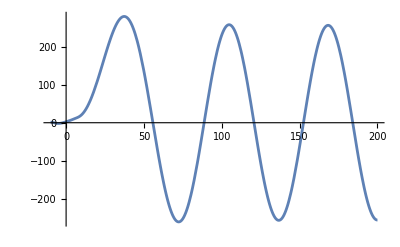

```mathematica
Plot[Re[zdata[x]],{x,-10,200}]
```

```mathematica
ωGrid=Table[0.01 j ,{j,1,3}];(*Table of energies where to evaluete the GBF*)
```

```mathematica
ClearAll[fitFarWaveSNExtremal,genGBspinM2];

fitFarWaveSNExtremal[Zfun_,ω_?NumericQ,{x1_?NumericQ,x2_?NumericQ},n_Integer:400]:=Module[{xData,yData,mat,coeffs,resid},xData=Subdivide[x1,x2,n];
yData=Zfun/@xData;
mat=Transpose@{Exp[I ω xData],Exp[-I ω xData]};
coeffs=LeastSquares[mat,yData];
resid=Norm[mat.coeffs-yData]/Norm[yData];
<|"Aout"->coeffs[[1]],"Ain"->coeffs[[2]],"Residual"->resid,"xData"->xData,"yData"->yData|>]


genGBspinM2[ωList_,l_,m_,xmin_,xmax_,fitWidth_:100,nFit_Integer:400]:=Module[{kH},Table[Module[{ω,Zfun,fit,x1,x2},ω=ωList[[j]];
kH=ω-m/(2 M);
Zfun=NDSolveValue[{Z''[x]+(ω^2-VeffInter[ω,m,l][x]) Z[x]==0,(*likely horizon condition*)Z[xmin]==Exp[-I kH xmin],Z'[xmin]==-I kH Exp[-I kH xmin]},Z,{x,xmin,xmax}];
x1=xmax-fitWidth;
x2=xmax;
fit=fitFarWaveSNExtremal[Zfun,ω,{x1,x2},nFit];
<|"ω"->ω,"Aout"->fit["Aout"],"Ain"->fit["Ain"],"Residual"->fit["Residual"],"Γ"->GBfromAinSNExtremal[fit["Ain"]]|>],{j,Length[ωList]}]]
```

```mathematica
data=genGBspinM2[ωGrid,2,2,xmin∞,xmax∞,100,500];
```

NDSolveValue::ndsz: At x == -1.58497×10^11, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {413.325} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {413.525} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {413.725} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolveValue::ndsz: At x == -1.58497×10^11, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolveValue::ndsz will be suppressed during this calculation.

```mathematica
xmax∞
```

513.325

```mathematica
xmin∞
```

-1.585×10^11

```mathematica
.
```

```mathematica
xmax∞
```

513.325

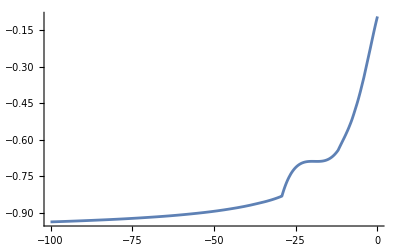

```mathematica
Plot[Re@VeffInter[1/100,2,2][x],{x,-100,0}]
```